# Comparison of single and double threshold networks with varying voting rule

This notebook compares the performance of single and double threshold networks as the voting rule is varied.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

09/08/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[ToFileName[path]];
ParallelEvaluate[AppendTo[$Path,path]];
ParallelEvaluate[<<definitions.m];
<<definitions.m
<<PlotLegends`
```

## Variables

Here, we define the parameters to be used:

```mathematica
M=200;
n=20;
v={20,15,9};
λ0=200;
δ=20;
snrdb=-10;
```

```mathematica
γ=10^(snrdb/10);
```

## Calculations

Calculate the performance of single and double threshold networks:

```mathematica
singleThresholdData=Table[{k,FusionCenterProbabilityOfFalseAlarm[ProbabilityOfFalseAlarm[M,λ0],n,k]+1-FusionCenterProbabilityOfDetection[ProbabilityOfDetection[M,γ,λ0],n,k]}//N,{k,n}];
```

```mathematica
doubleThresholdData=Table[{k,FusionCenterProbabilityOfFalseAlarm[{ProbabilityOfAcquisition[M,λ0],1-ProbabilityOfFalseAlarm[M,λ0+δ]-ProbabilityOfAcquisition[M,λ0],ProbabilityOfFalseAlarm[M,λ0+δ]},v0,k]+1-FusionCenterProbabilityOfDetection[{ProbabilityOfMissedDetection[M,γ,λ0],1-ProbabilityOfDetection[M,γ,λ0+δ]-ProbabilityOfMissedDetection[M,γ,λ0],ProbabilityOfDetection[M,γ,λ0+δ]},v0,k]}//N,{v0,v},{k,v0}];
```

## Results

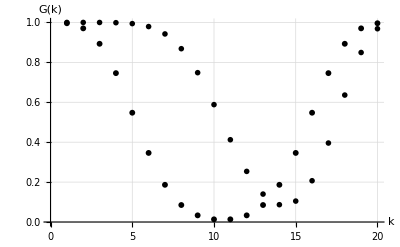
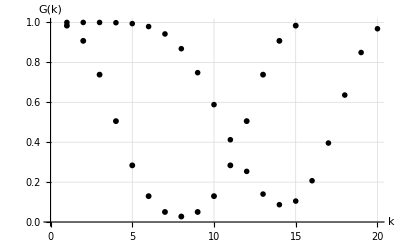
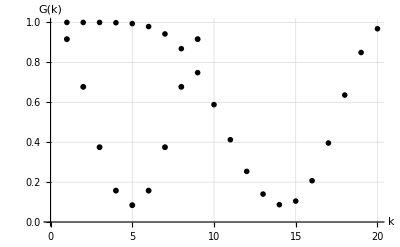

```mathematica
Table[ListPlot[{doubleThresholdData[[i]],singleThresholdData},AxesLabel->{"k","G(k)"},PlotRange->{{0,n},{0,1}},PlotStyle->Black,PlotMarkers->{Graphics[Disk[],ImageSize->6],Graphics[GraphicsComplex[{{1,0},{0,1},{-1,0},{0,-1}},Line[{1,2,3,4,1}]],ImageSize->7]},PlotLegend->{"Double threshold","Single threshold"},LegendSize->{0.65,0.3},LegendTextSpace->5,LegendPosition->{-0.04,0.23},LegendShadow->None,GridLines->Automatic,ImageSize->400],{i,Length[v]}]
```